```mathematica
(* Mathematica*)
```

```mathematica
(* Fano Projerctive Plane as 7 Killing vectors group*)
```

```mathematica
(*incidence matrix is[1 1 1 0 0 0 0;1 0 0 1 1 0 0;1 0 0 0 0 1 1;0 1 0 1 0 1 0;0 1 0 0 1 0 1;0 0 1 1 0 0 1;0 0 1 0 1 1 0*)
```

```mathematica
s[1]={1,1 ,1 ,0,0 ,0 ,0}
s[2]={1 ,0 ,0 ,1,1, 0 ,0}
s[3]={1 ,0 ,0 ,0 ,0 ,1,1}
s[4]={0 ,1 ,0 ,1, 0, 1,0}
s[5]={0 ,1 ,0 ,0,1 ,0 ,1}
s[6]={0, 0 ,1 ,1 ,0, 0 ,1}
s[7]={0 ,0, 1,0,1 ,1,0}
```

{1,1,1,0,0,0,0}

{1,0,0,1,1,0,0}

{1,0,0,0,0,1,1}

{0,1,0,1,0,1,0}

{0,1,0,0,1,0,1}

{0,0,1,1,0,0,1}

{0,0,1,0,1,1,0}

```mathematica
ka=Table[s[i],{i,7}]
```

{{1,1,1,0,0,0,0},{1,0,0,1,1,0,0},{1,0,0,0,0,1,1},{0,1,0,1,0,1,0},{0,1,0,0,1,0,1},{0,0,1,1,0,0,1},{0,0,1,0,1,1,0}}

```mathematica
ga=GraphPlot3D[ka,ImageSize->2000];
```

```mathematica
Eigenvalues[ka]
```

{3,-√2,-√2,-√2,√2,√2,√2}

```mathematica
Table[Tr[s[i]],{i,7}]
```

{3,3,3,3,3,3,3}

```mathematica
(* Casimir Invariant*)
```

```mathematica
Sum[s[i].s[i],{i,7}]
```

21

```mathematica
(* orthogonality "zero": singularity/ punctured Polyhedron *)
```

```mathematica
Sum[s[i].Transpose[s[i]],{i,7}]
```

21

```mathematica
ka.Transpose[ka]
```

{{3,1,1,1,1,1,1},{1,3,1,1,1,1,1},{1,1,3,1,1,1,1},{1,1,1,3,1,1,1},{1,1,1,1,3,1,1},{1,1,1,1,1,3,1},{1,1,1,1,1,1,3}}

```mathematica
Transpose[ka].ka
```

{{3,1,1,1,1,1,1},{1,3,1,1,1,1,1},{1,1,3,1,1,1,1},{1,1,1,3,1,1,1},{1,1,1,1,3,1,1},{1,1,1,1,1,3,1},{1,1,1,1,1,1,3}}

```mathematica
ca=Table[2*ka[[i]].ka[[j]]/(ka[[i]].ka[[i]]),{i,7},{j,7}]
```

{{2,2/3,2/3,2/3,2/3,2/3,2/3},{2/3,2,2/3,2/3,2/3,2/3,2/3},{2/3,2/3,2,2/3,2/3,2/3,2/3},{2/3,2/3,2/3,2,2/3,2/3,2/3},{2/3,2/3,2/3,2/3,2,2/3,2/3},{2/3,2/3,2/3,2/3,2/3,2,2/3},{2/3,2/3,2/3,2/3,2/3,2/3,2}}

```mathematica
Det[ca]
```

8192/243

```mathematica
Tr[ca]
```

14

```mathematica
TableForm[ca]
```

2 | 2/3 | 2/3 | 2/3 | 2/3 | 2/3 | 2/3
2/3 | 2 | 2/3 | 2/3 | 2/3 | 2/3 | 2/3
2/3 | 2/3 | 2 | 2/3 | 2/3 | 2/3 | 2/3
2/3 | 2/3 | 2/3 | 2 | 2/3 | 2/3 | 2/3
2/3 | 2/3 | 2/3 | 2/3 | 2 | 2/3 | 2/3
2/3 | 2/3 | 2/3 | 2/3 | 2/3 | 2 | 2/3
2/3 | 2/3 | 2/3 | 2/3 | 2/3 | 2/3 | 2

```mathematica
Eigenvalues[ca]
```

{6,4/3,4/3,4/3,4/3,4/3,4/3}

```mathematica
p[x_]=ExpandAll[CharacteristicPolynomial[ca,x]]
```

8192/243-(114688 x)/729+(25088 x^2)/81-(8960 x^3)/27+(5600 x^4)/27-(224 x^5)/3+14 x^6-x^7

```mathematica
Discriminant[p[x],x]
```

0

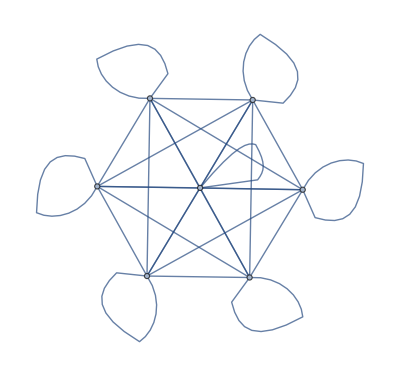

```mathematica
WeightedAdjacencyGraph[ca]
```

```mathematica
caj=Floor[Abs[ca]]
```

{{2,0,0,0,0,0,0},{0,2,0,0,0,0,0},{0,0,2,0,0,0,0},{0,0,0,2,0,0,0},{0,0,0,0,2,0,0},{0,0,0,0,0,2,0},{0,0,0,0,0,0,2}}

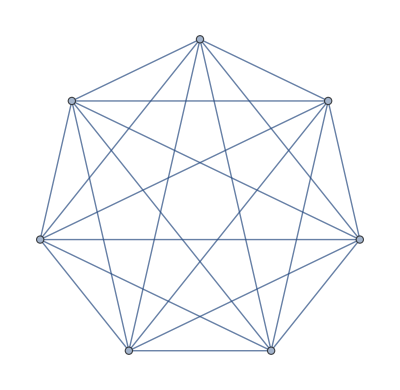

```mathematica
GraphPlot[ca]
```

```mathematica
GraphPlot3D[ca]
```

-Graphics3D-

```mathematica
(*end*)
```

```mathematica
(* incidence  matrix*)
```

```mathematica
M0=ka
```

{{1,1,1,0,0,0,0},{1,0,0,1,1,0,0},{1,0,0,0,0,1,1},{0,1,0,1,0,1,0},{0,1,0,0,1,0,1},{0,0,1,1,0,0,1},{0,0,1,0,1,1,0}}

```mathematica
MatrixForm[M0]
```

(1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1 | 0)

```mathematica
(* graph from  Adjacency Matrix*)
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
g0=FromAdjacencyMatrix[M0]
```

⁃Graph:<12,7,Undirected>⁃

```mathematica
ga=GraphPlot3D[M0,ImageSize->2000];
```

```mathematica
ShowGraph[g0];
```

```mathematica
g1=Show[GraphPlot3D[g0],ImageSize->Full];
```

```mathematica
(* make polynomial*)
```

```mathematica
CharacteristicPolynomial[M0,x]
```

-24+8 x+36 x^2-12 x^3-18 x^4+6 x^5+3 x^6-x^7

```mathematica
(* solve Polynomial*)
```

```mathematica
w=x/.NSolve[CharacteristicPolynomial[M0,x]==0,x]
```

{-1.41421,-1.41421,-1.41421,1.41421,1.41421,1.41421,3.}

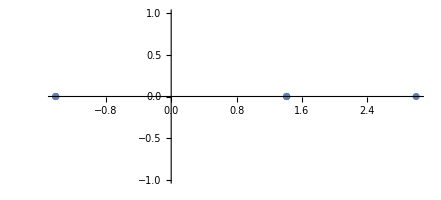

```mathematica
ComplexListPlot[w]
```

```mathematica
r[i_]:={Re[x],Im[x]}/.NSolve[CharacteristicPolynomial[M0,x]==0,x][[i]]
```

```mathematica
Clear[s]
```

```mathematica
(*For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/FanoPlane.html.*)
e={{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}
{{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}
```

{{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}

{{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}

```mathematica
Table[s[i]=e[[i]],{i,7}]
```

{{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}

```mathematica
w=Flatten[Table[s[i],{i,7}]]
```

{1,7,5,2,7,6,3,7,4,1,6,3,3,5,2,1,4,2,4,5,6}

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[9];
```

```mathematica
Length[aa]
```

413343

```mathematica
(*{{"Dipyramid",5},Show[-Graphics3D-,ImageSize->2000],7,10,15,GraphicsComplex[{{0,0,-√(1/10 (5-√5))},{0,0,√(1/10 (5-√5))},{√(1/2+1/(2 √5)),0,0},{1/2 √(1/10 (5-√5)),1/4 (-1-√5),0},{1/2 √(1/10 (5-√5)),1/4 (1+√5),0},{-√(1/4+1/(2 √5)),-1/2,0},{-√(1/4+1/(2 √5)),1/2,0}},Polygon[…]]}*)
```

```mathematica
v=N[{{0,0,-√(1/10 (5-√5))},{0,0,√(1/10 (5-√5))},{√(1/2+1/(2 √5)),0,0},{1/2 √(1/10 (5-√5)),1/4 (-1-√5),0},{1/2 √(1/10 (5-√5)),1/4 (1+√5),0},{-√(1/4+1/(2 √5)),-1/2,0},{-√(1/4+1/(2 √5)),1/2,0}}];
```

```mathematica
r[i_]:=v[[i]]
```

```mathematica
bb=aa /. 1->r[1]/. 2->r[2]/. 3-> r[3] /. 4->r[4]/. 5->r[5]/. 6->r[6]/. 7->r[7];
```

```mathematica
cc=FoldList[Plus,{0,0,0},bb];
```

```mathematica
g1=ListPointPlot3D[cc,ColorFunction->"Rainbow",ImageSize->2000,PlotStyle->PointSize[0.001],Background->Black,ViewPoint->{2,2,2}];
```

```mathematica
g2=Show[g1,ViewPoint->Above];
```

```mathematica
g3=Show[g1,ViewPoint->{1.3, -2.4, 2.}];
```

```mathematica
g4=Show[g1,ViewPoint->Right];
```

```mathematica
g5=Show[g1,ViewPoint->Back];
```

```mathematica
Export["7symbol_2nd_Order_ProjectivePlane_Substitution_Level9_graph_Polyhedron2_5views.jpg",{ga,g1,g2,g3,g4,g5}]
```

```mathematica
(*end*)
```